# Signal Processing - Project 1

## William Lewin & Elias Chahine wlewin@kth.se echahine@kth.se

## Part 1

### Assignment

A mobile station is moving along a straight line, away from a basestation at position x=0. The basestation antenna is at 30m above the ground and the mobile antenna is at 1.5 m. As seen by the picture the mobile is receiving two signals one direct ray and one reflected. Assume that the reflection is perfect which means no power loss at the reflection, but a phase shift of π.

Plot the squared amplitude (power) of the received signal when the mobile is moving from position x=0 to x=2km. Experiment with different types of graphs (e.g. log-scale, dB etc) to get a nice picture.

### Discussion

The problem at hand is to examine the effect of line-of-sight propagation of wireless signals.

When the car travels from 0 to 2000m away from the antenna, both the reflected and the direct signal changes. 

The recieved signal can be interpereted as the sum of both the reflected and the direct signal.

### Code

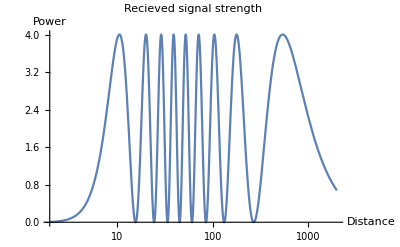

```mathematica
ClearAll["`*"]
f=900*10^6; (*Frequency*)
c=299792458; (*Speed of light*)
ω=2*Pi*f;
th=30; (*Tower height*)
ch=1.5; (*Height of the car-antenna*)

(*Pythagoran theorem*)

(*Direct from tower to car: *)
distance1[x_]:=√((th-ch)^2+x^2);
(*Reflected from tower to car: *)
distance2[x_]:=√((th+ch)^2+x^2);


(* Time taken for the signal to reach the car at both signals *)
time1[x_]=distance1[x]/c;
time2[x_]= distance2[x]/c;
(*Direct signal*)
signal1[t_]:=ⅇ^(ⅉ(ω*t)); 
(*Reflected signal, Phase shifted direct signal*)
signal2[t_]:=ⅇ^(ⅉ(ω*t+Pi)); 

(*Recieved signal, from assignment*)
recieved[t_, x_]:=signal1[t-time1[x]]+signal2[t-time2[x]] ;

(*Remove imaginary part from signal*)
remove[x_]:=Simplify[ExpandAll[ⅇ^(-ⅉ*ω*t)recieved[t,x]]];
amplitude[x_]:=(Abs[remove[x]])^2;
LogLinearPlot[amplitude[x],{x,0,2000}, PlotLabel->"Recieved signal strength", AxesLabel->{"Distance", "Power"}]
```

## Part 2

### Assignment

### Discussion

### Code